# Fock State Amplification - CASR

## Last Updated: 2025/10/22 v1.1.3

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

## Options

```mathematica
(*set analytical plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[LogLogPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set list plot options*)
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set bar/histogram plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Plot Creation

```mathematica
(*get default plot colors*)
DefaultPlotColors=Cases[#,_?ColorQ,All]&["DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme[Automatic,Plot])];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## Phonon Conversion

### Coherent_C

```mathematica
(*coherent_c: convert R/B ratio to <n> assuming a coherent state*)
```

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{0.,0.791977}},{5,7,0,{102},{4},0,0,0,0,Automatic,«3»},{{0.,0.0000999968,0.000399949,0.000899744,0.00159919,0.00249802,0.0035959,0.00489242,0.00638707,0.00807931,«92»}},{Developer`PackedArrayForm,{0,1,2,3,4,5,6,7,8,9,«93»},{0.,0.0001,0.0004,0.0009,0.0016,0.0025,0.0036,0.0049,0.0064,0.0081,«92»}},{Automatic}][x_] is Protected.

### Coherent_R

```mathematica
(*coherent_c: convert RSB probability ONLY to <n> assuming a coherent state*)
```

```mathematica
coherentR0={
0,9.99931658497433*^-5,0.000399890663733249,0.000899446570690410,0.00159825126849689,0.00249573182347329,0.00359115251770981,0.00488361553119066,0.00637206177417027,0.00805527186899924,0.00993186728045770,0.0120003115935124,0.0142589119372707,0.0167058205537671,0.0193390365100727,0.0221564075520917,0.0251556320982592,0.0283342613712326,0.0316897016655309,0.0352192167489441,0.0389199303954148,0.0427888290469539,0.0468227646020514,0.0510184573278918,0.0553724988935951,0.0598813555215709,0.0645413712539629,0.0693487713310517,0.0742996656783876,0.0793900524992962,0.0846158219693280,0.0899727600291077,0.0954565522719444,0.101062787922491,0.106786963902628,0.112624488980697,0.118570688000088,0.124620806183157,0.130770013506336,0.137013409142264,0.143346025964675,0.149762835111746,0.156258750603538,0.162828634009109,0.169467299158846,0.176169516897511,0.182930019873458,0.189743507359448,0.196604650100454,0.203508095183842,0.210448470927264,0.217420391779606,0.224418463230326,0.231437286722481,0.238471464564783,0.245515604837990,0.252564326290965,0.259612263221736,0.266654070338924,0.273684427598902,0.280698045014097,0.287689667427855,0.294654079251349,0.301586109158018,0.308480634731091,0.315332587059793,0.322136955279870,0.328888791054132,0.335583212988793,0.342215410981400,0.348780650496278,0.355274276763424,0.361691718896910,0.368028493928910,0.374280210755539,0.380442573990817,0.386511387725119,0.392482559184592,0.398352102288109,0.404116141098438,0.409770913164383,0.415312772750811,0.420738193953524,0.426043773696107,0.431226234605960,0.436282427766861,0.441209335345508,0.446004073089648,0.450663892695473,0.455186184042142,0.459568477291385,0.463808444850291,0.467903903195516,0.471852814557270,0.475653288461590,0.479303583129547,0.482802106732168,0.486147418499979,0.489338229686260,0.492373404383192,0.495251960190268,0.497973068734440,0.500536056041652,0.502940402759546,0.505185744231242,0.507271870420298,0.509198725687029,0.510966408416576,0.512575170499202,0.514025416663485,0.515317703663170,0.516452739318639,0.517431381414049,0.518254636451358,0.518923658262584,0.519439746481792,0.519804344878417,0.520019039553689,0.520085557002049,0.520005762039560,0.519781655601477,0.519415372411236,0.518909178523259,0.518265468742100,0.517486763920557,0.516575708139507,0.515535065772334,0.514367718436921,0.513076661838286,0.511665002505056,0.510135954423077,0.508492835569525,0.506739064351023,0.504878155949329,0.502913718578252,0.500849449655556,0.498689131893661,0.496436629313061,0.494095883182420,0.491670907889407,0.489165786746364,0.486584667734993,0.483931759194270,0.481211325455891,0.478427682431564,0.475585193156511,0.472688263293616,0.469741336602651,0.466748890379059,0.463715430866808,0.460645488649837,0.457543614026645,0.454414372372584,0.451262339494410,0.448092096981688,0.444908227559604,0.441715310447763,0.438517916729525,0.435320604736432,0.432127915452247,0.428944367941117,0.425774454804329,0.422622637670119,0.419493342720928,0.416390956262505,0.413319820339149,0.410284228399400,0.407288421016389,0.404336581667029,0.401432832574140,0.398581230615570,0.395785763304283,0.393050344843310,0.390378812259402,0.387774921619125,0.385242344331059,0.382784663537692,0.380405370600468,0.378107861681413,0.375895434424601,0.373771284740682,0.371738503697539,0.369800074520074,0.367958869701985,0.366217648232303,0.364579052939329,0.363045607954507,0.361619716298632,0.360303657592692,0.359099585895489,0.358009527670097,0.357035379881037,0.356178908223974,0.355441745489547,0.354825390062886,0.354331204560147,0.353960414603333,0.353714107734502,0.353593232470306,0.353598597497709,0.353730871011554};
```

```mathematica
coherentRX0=Range[0.,2.,2./(Length[coherentR0]-1)]^2.;
```

```mathematica
(*note: need to truncate after 120 points b/c curve is non-injective after that*)
CoherentRFunc=Interpolation[Transpose[{coherentR0,coherentRX0}][[;;120]]];
CoherentR[x_]:=CoherentRFunc[#]&[Clip[x,{0.,0.6}]];
```

### Coherent_ARP

```mathematica
(*todo: account for n != 0*)
CoherentARP[P_,n_:0]:=-Log[P+1.*^-7];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
(*also returns the *)
CollateData2[dataset_List,groupColumnList_List]:=GroupBy[
(*apply to dataset*)
dataset,

(*grouping functions: functions to group successively/nested*)
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
]
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

# Quick MultiPlots

## Bar Charts/Histograms

## Raw Data

```mathematica
(*(*RIDs 130724 - 130727*)
fockCompareData={
{0,297.278},
{1,206.742},
{2,156.077},
{3,157.983}
};*)
```

```mathematica
(*(*RIDs 130728 - 130731*)
fockCompareData={
{0,437.922},
{1,282.368},
{2,206.861},
{3,202.126}
};*)
```

```mathematica
(*(*RIDs 130402, 130406 - 130408*)
fockCompareData={
{0,0.07239,0.0044},
{1,0.198611,0.0120502},
{2,0.299764,0.0108691},
{3,0.320936,0.0128084}
};*)
```

```mathematica
(*RIDs 134683-134711, 134757-134767*)
fockCompareData={
{0,58.59,9.46},
{1,30.91,4.70},
{2,21.75,1.28},
{3,13.21,0.68}
};
```

```mathematica
(*(*RIDs 134887 - 134890*)
fockCompareData={
{0,335.39},
{1,200.63},
{2,148.76},
{3,141.99}
};*)
```

```mathematica
(*(*RIDs 134912 - 134915*)
fockCompareData={
{0,0.8747,0.038},
{1,0.663,0.03},
{2,0.537,0.02},
{3,0.4144,0.02}
};*)
```

## Process

```mathematica
(*need to rescale data for bar chart lmao*)
fockCompareData[[;;,1]]+=1;
```

## Analytical ListPlot

```mathematica
(*create analytical data for listplot*)
fockAnalyticalData=fockCompareData[[;;,{1,2}]];
fockAnalyticalData[[;;,2]]=fockAnalyticalData[[1,2]]*√(4/(8*(fockAnalyticalData[[;;,1]]-1)+4));
(*fockAnalyticalData[[;;,2]]=fockAnalyticalData[[1,2]]*(8*(fockAnalyticalData[[;;,1]]-1)+4)/4(*√((8*(fockAnalyticalData[[;;,1]]-1)+4)/4)*);*)
```

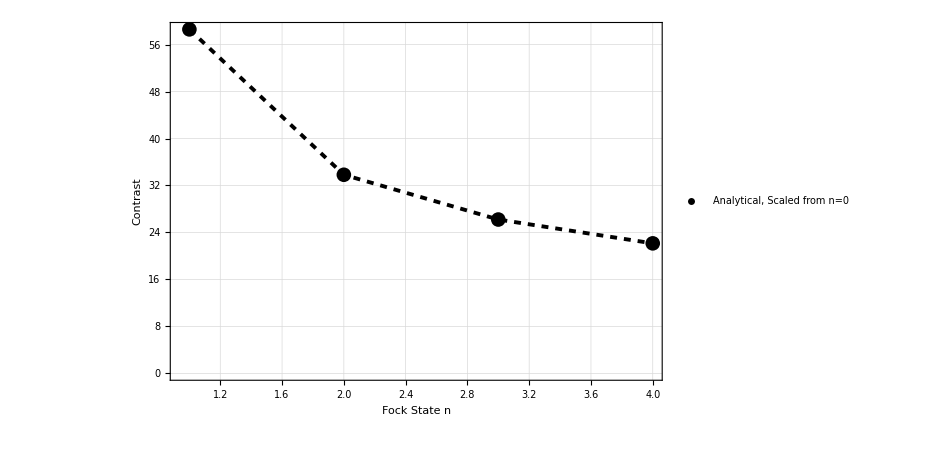

```mathematica
(*plot analytical form via listplot*)
fockAnalyticalPlot=ListPlot[
{
fockAnalyticalData,
fockAnalyticalData
},
PlotRange->{
{Full,Full},
{0.,Full}
},

FrameLabel->{ 
{Style["Contrast",{Black,Directive[15]}],None},
{
Style["Fock State n",{Black,Directive[15]}],
Style["Fock Amplification - Metrological Gain",{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},

PlotLegends->{
"Analytical, Scaled from n=0"
},

ImageSize->{700,450},
AspectRatio->Full
]
```

## Bar Chart Fock Data

```mathematica
(*convert to around*)
fockCompareDataPlot=Transpose[{fockCompareData[[;;,1]],Around@@@fockCompareData[[;;,{2,3}]]}];
(*(*normal/no around*)
fockCompareDataPlot=Transpose[{fockCompareData[[;;,1]],fockCompareData[[;;,2]]}];*)
```

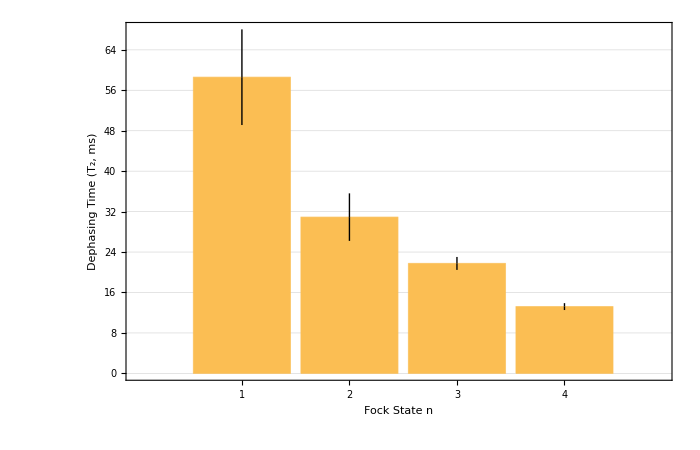

```mathematica
fockCompareBarPlot=BarChart[
fockCompareDataPlot[[;;,2]],

ChartLabels->Range[
Min[fockCompareData[[;;,1]]],
Max[fockCompareData[[;;,1]]]
],
PlotRange->{
{Full,Full},
{0.,Full}
},

FrameLabel->{ 
{Style["Dephasing Time (T_2, ms)",{Black,Directive[15]}],None},
{
Style["Fock State n",{Black,Directive[15]}],
Style["Fock Amplification - Decoherence (Axial)",{Black,Directive[15]}]
}
},

ImageSize->{700,450},
AspectRatio->Full
]
```

## Summary Plot

```mathematica
fockCompareSummaryPlot=Show[{
fockCompareBarPlot
(*fockAnalyticalPlot*)
}];
```

## Show

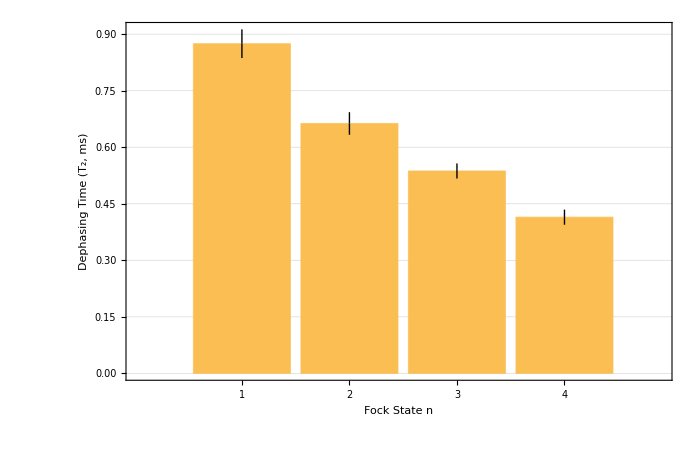

```mathematica
fockCompareSummaryPlot
```

## Phase MultiPlot

```mathematica
dsPhase3=First@dsRawPlot;
```

```mathematica
tmpPhaseFockPlot=ListPlot[
{
dsPhase0,dsPhase0,
dsPhase1,dsPhase1,
dsPhase2,dsPhase2,
dsPhase3,dsPhase3
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Probability (P_D)",{Black,Directive[15]}],None},
{
Style[StringForm["Signal Phase (turns)"],{Black,Directive[15]}],
Style[StringForm["Fock Amplification - Phase"],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.015]},
{DefaultPlotColors[[1]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[2]],PointSize[0.015]},
{DefaultPlotColors[[2]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[3]],PointSize[0.015]},
{DefaultPlotColors[[3]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[4]],PointSize[0.015]},
{DefaultPlotColors[[4]],(*Dashed,*)Thickness[0.004]}
},
Joined->{False,True,False,True,False,True,False,True},
ImageSize->Scaled[0.45]
]
```

## Linescan Multiple Plot

```mathematica
fitFreq3=fitRes;
dsFreq3=dsRawPlot;
```

```mathematica
tmpFreqFockFitPlot=Plot[
{
fitFreq0[δ],
fitFreq1[δ],
fitFreq2[δ],
fitFreq3[δ]
},
{δ,dsN[[1,1]],dsN[[-1,1]]},
PlotRange->Full,
PlotStyle->{
{DefaultPlotColors[[1]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[2]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[3]],(*Dashed,*)Thickness[0.004]},
{DefaultPlotColors[[4]],(*Dashed,*)Thickness[0.004]}
}
]
```

```mathematica
tmpFreqFockDataPlot=ListPlot[
{
dsFreq0,(*dsFreq0,*)
dsFreq1,(*dsFreq1,*)
dsFreq2,(*dsFreq2,*)
dsFreq3(*dsFreq3*)
},
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Probability (P_D)",{Black,Directive[15]}],None},
{
Style[StringForm["Signal Detuning (kHz)"],{Black,Directive[15]}],
Style[StringForm["Fock Amplification - Linescan"],{Black,Directive[15]}]
}
},

PlotStyle->{
{DefaultPlotColors[[1]],PointSize[0.015]},
(*{DefaultPlotColors[[1]],(*Dashed,*)Thickness[0.004]},*)
{DefaultPlotColors[[2]],PointSize[0.015]},
(*{DefaultPlotColors[[2]],(*Dashed,*)Thickness[0.004]},*)
{DefaultPlotColors[[3]],PointSize[0.015]},
(*{DefaultPlotColors[[3]],(*Dashed,*)Thickness[0.004]},*)
{DefaultPlotColors[[4]],PointSize[0.015]}
(*{DefaultPlotColors[[4]],(*Dashed,*)Thickness[0.004]}*)
},
Joined->{False,(*True,*)False,(*True,*)False,(*True,*)False(*,True*)},
ImageSize->Scaled[0.45]
]
```

```mathematica
Show[
{tmpFreqFockDataPlot,tmpFreqFockFitPlot}
]
```

# Displacement Sweep

```mathematica
(*todo: also plot displacement sweeps*)
```

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2025-10\\2025-10-18";
```

```mathematica
(*specify datasets*)
ridList={134627};(*list of RIDs*)
```

```mathematica
(*specify fock state du jour*)
nDJ=3;
```

## Import & Process

## Configuration

Dataset Configuration:

```mathematica
freqReadoutCol=1;(*729nm readout freq - used for SBR readout*)
```

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=7;(*sweep column*)
```

Convert Units:

```mathematica
freqReadoutUnits=ftwToFrequencyMHz;(*convert from readout frequency to target units*)
```

```mathematica
(*time to displacement conversion*)
sweepUnits=0.011774*240;(*convert sweep column to target units*)
```

Processing Configuration:

```mathematica
procStyle="729";(*sideband ratio: "SBR", RAP: "RAP", 729: "729"*)
```

Plotting Configuration:

```mathematica
xAxisLabel="Displacement (α)";(*x-axis label for sweep*)
figureTitle="Displacement Readout";(*plot title to set*)
```

## Import

```mathematica
(*import raw dataset*)
datafileList=ImportDatasetARTIQ[directoryString,ToString[#]]&/@ridList;
```

```mathematica
(*merge datasets and get parameter list*)
dataset=Join@@(First/@datafileList);
parameters=(First@datafileList)[[2]];
```

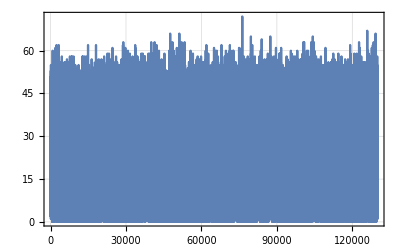
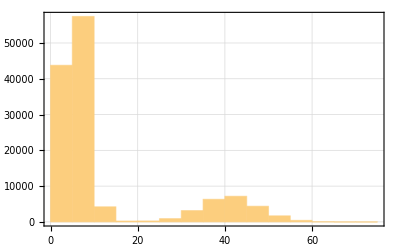
{(-1. | 46. | 8.6×10^7 | 0. | 0. | 0. | 0. | 0.1247 | 256.
-1. | 8. | 8.6×10^7 | 0. | 0. | 0. | 0.12 | 0.1247 | 256.
-1. | 7. | 8.6×10^7 | 0. | 0. | 0. | 0.96 | 0.1247 | 256.),-Graphics-,-Graphics-}

```mathematica
(*plot important stuff*)
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
{
(*parameters["att_squeeze_db"],
parameters["enable_antisqueezing"]*)
};
```

## Preprocess

```mathematica
(*threshold counts (via auto histogram-based method)*)
datasetProcessed=ThresholdCounts[
dataset[[;;,{freqReadoutCol,sweepCol,countCol}]],
3
];

(*convert dataset units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{freqReadoutUnits,sweepUnits,1}
];
```

## Configured Processing

```mathematica
(*process results specific to each experiment type*)
Switch[procStyle,
"SBR",
	(*process rsb and bsb*)
	freqCenter=Mean[datasetProcessed[[;;,1]]];
	dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
	dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
	{dsR,dsB}=CollateDataSimple[#,{1}]&/@{dsR,dsB};

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsR[[;;,3]]=dsR[[;;,3]]/.{(0|0.)->0.01};
	dsR=Transpose[{dsR[[;;,1]],Around@@@dsR[[;;,{2,3}]]}];
	dsB[[;;,3]]=dsB[[;;,3]]/.{(0|0.)->0.01};
	dsB=Transpose[{dsB[[;;,1]],Around@@@dsB[[;;,{2,3}]]}];

	(*process phonon number*)
	dsN=dsR;dsN[[;;,2]]/=dsB[[;;,2]];
	dsNValTMP=CoherentC[#["Value"]&/@dsN[[;;,2]]];
	dsNErrTMP=CoherentCErr[#["Uncertainty"]&/@dsN[[;;,2]]];
	dsNErrTMP=(#*CoherentCErr[#])&/@(#["Uncertainty"]&/@dsN[[;;,2]]);

	(*final plotting preparation*)
	dsRawPlot={dsR,dsR,dsB,dsB};
	dsConfiguredYLabel="⟨n⟩";,

"RAP",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsN[[;;,2]]=CoherentARP[1.-dsN[[;;,2]]];,
	dsConfiguredYLabel="⟨n⟩";

"729",
	(*collate dataset*)
	dsN=CollateDataSimple[
	datasetProcessed[[;;,{2,3}]],
	{1}
	];

	(*replace 0 uncertainties with some minimum value then convert to Around*)
	dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};
	dsN=Transpose[{dsN[[;;,1]],Around@@@dsN[[;;,{2,3}]]}];

	(*final plotting preparation*)
	dsRawPlot={dsN,dsN};
	dsConfiguredYLabel="Dark-State Probability (P_D)";
];
```

## Fit

```mathematica
(*separate out values from uncertainty (b/c fit functions can't take Around)*)
dsFitVals={#[[1]],#[[2]]["Value"]}&/@dsN;
dsFitWeights=(#[[2]]["Uncertainty"]&/@dsN)^-2.;
```

## Prepare Fitting

```mathematica
(*fit function*)
fitfunc=ADJ*(1.-Exp[-#^2.]*LaguerreL[nDJ,#^2]^2.)+CDJ&[dαdt*t];
```

```mathematica
(*set fitting constraints*)
fitConstraintsDJ={
0.<=ADJ<=1.,
0.<=CDJ<=1.
};
```

```mathematica
(*guess fit parameters*)
fitGuessDJ={
{ADJ,1.-Min[dsFitVals[[;;,2]]]},(*probability contrast*)
{CDJ,Min[dsFitVals[[;;,2]]]},(*probability offset*)
{dαdt,0.01}(*linecenter*)
}
```

{{ADJ,0.8422},{CDJ,0.1578},{dαdt,0.01}}

## Fit & Extract Results

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsFitVals,
Join[{fitfunc},fitConstraintsDJ],
fitGuessDJ,
t,
Weights->dsFitWeights
];
]
```

{0.0220369,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

## Raw Data

```mathematica
(*raw probability plot*)
dataProbPlot=ListPlot[
dsRawPlot,
PlotRange->{
{Automatic,Automatic},
{0.,1.}
},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Red,PointSize[0.015]},
{Red,Dashed,Thickness[0.004]},
{Blue,PointSize[0.015]},
{Blue,Dashed,Thickness[0.004]}
},
Joined->{False,True,False,True},
ImageSize->Scaled[0.45]
];
```

## Processed Data

```mathematica
(*phonon plot*)
dataPhononPlot=ListPlot[
{
dsN,dsN
},
PlotRange->{
{Automatic,Automatic},
{0.,(*Automatic*)(*Full*)1.}
},
FrameLabel->{ 
{Style[dsConfiguredYLabel,{Black,Directive[15]}],None},
{
Style[StringForm["``",xAxisLabel],{Black,Directive[15]}],
Style[StringForm["`` (``) - RID: ``",figureTitle,procStyle,ridList],{Black,Directive[15]}]
}
},

PlotStyle->{
{Black,PointSize[0.015]},
{Black,Dashed,Thickness[0.004]}
},
Joined->{False,True},
ImageSize->Scaled[0.45]
];
```

## Fit Results

```mathematica
(*plot fitted results*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,0.,dsN[[-1,1]]},
PlotRange->Full
];
```

## Summary Figure

```mathematica
(*combine summary figure*)
summaryFigure={
(*processed data*)
Show[{
dataPhononPlot,
fitPlot
}
],
dataProbPlot
};
```

## Show

| Estimate | Standard Error | Confidence Interval
ADJ | 0.789713 | 0.00871802 | {0.771679,0.807748}
CDJ | 0.155418 | 0.00807508 | {0.138714,0.172123}
dαdt | -0.966551 | 0.00533552 | {-0.977589,-0.955514}

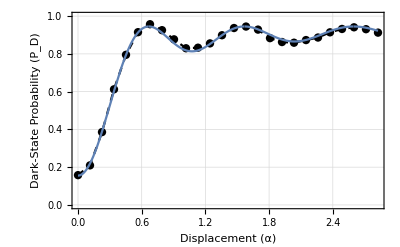
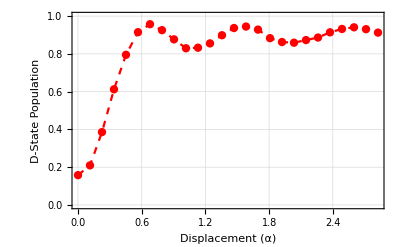

```mathematica
fitParams
summaryFigure
```

## Process Fisher Information

```mathematica
(*dsOld3=First@dsRawPlot;
fitOld3=fitRes;*)
```

```mathematica
(*convert uncertainty from stderr to stdev for FI calc*)
numAverages=5000;
```

```mathematica
(*create association of relevant datasets and fits*)
dataDisplaceAssoc=<|"n=0"->ds0,"n=1"->ds1,"n=2"->ds2,"n=3"->ds3|>;
fitDisplaceAssoc=<|"n=0"->fit0,"n=1"->fit1,"n=2"->fit2,"n=3"->fit3|>;
(*dataDisplaceAssoc=<|"n=0"->dsOld0,"n=1"->dsOld1,"n=2"->dsOld2,"n=3"->dsOld3|>;
fitDisplaceAssoc=<|"n=0"->fitOld0,"n=1"->fitOld1,"n=2"->fitOld2,"n=3"->fitOld3|>;*)
```

## Fisher Information Processing Functions

```mathematica
(*calculate FI using data w/ analytical uncertainties (from bernoulli)*)
Clear[FisherInformationExpInterp];
FisherInformationExpAnal[data_List]:=(Interpolation[data]'/@data[[;;,1]])^2./(data[[;;,2]]*(1.-data[[;;,2]]));
```

```mathematica
(*calculate FI using data w/ experimental uncertainties - interpolation*)
Clear[FisherInformationExpInterp];
FisherInformationExpInterp[data_List,unc_List]:=(Interpolation[data]'/@data[[;;,1]])^2./(unc)^2.;
```

```mathematica
(*calculate FI using data w/ experimental uncertainties - numerical*)
Clear[FisherInformationExpNum];
FisherInformationExpNum[data_List,numAvgs_]:=Module[
{
scoreData=Join[
(*first point - asymmetric difference quotient*)
{{data[[1,1]],(data[[2,2]]-data[[1,2]])/(data[[2,1]]-data[[1,1]])}},

(*other points - symmetric difference quotient*)
Transpose[{
data[[2;;-2,1]],
(data[[3;;,2]]-data[[1;;-3,2]])/(data[[3;;,1]]-data[[1;;-3,1]])
}],

(*last point - asymmetric difference quotient again*)
{{data[[-1,1]],(data[[-1,2]]-data[[-2,2]])/(data[[-1,1]]-data[[-2,1]])}}
],

(*get variance of underlying probabilities*)
probVar=(#["Uncertainty"]&/@data[[;;,2]])^2.*numAvgs,

fisherInfoData
},
(*Print[probVar];
Print[scoreData];*)

fisherInfoData=scoreData;
fisherInfoData[[;;,2]]=(fisherInfoData[[;;,2]])^2./probVar;
Return[fisherInfoData];

];
```

```mathematica
(*calculate FI for fit functions*)
Clear[FisherInformationFunc];
FisherInformationFunc[func_,x_]:=(func'[x])^2./(func[x]*(1.-func[x]));
(*Clear[FisherInformationFunc2];
FisherInformationFunc2[func_]:=(func')^2./(func*(1.-func));*)
```

## Actual Process

```mathematica
(*calculate fisher info for data with around*)
dataFisherAssoc=FisherInformationExpNum[#,numAverages]&/@dataDisplaceAssoc;
```

```mathematica
(*calculate fisher info for fits*)
fitFisherAssoc=FisherInformationFunc[#,t]&/@fitDisplaceAssoc;
```

```mathematica
(*numerically calculate maxima of fisher info from processed fitted curves*)
dataBounds=(First@dataFisherAssoc)[[{1,-1},1]];
fisherFitMaximaRaw=NMaximize[
{
#,
dataBounds[[1]]<=t<=dataBounds[[-1]]
},
t
]&/@fitFisherAssoc;
(*format fisher info (fitted) maxima nicely*)
fisherFitMaximaFormatted=MatrixForm[
Transpose[
{
Keys[fisherMaxima],
Values[fisherMaxima]
}
]
];
```

```mathematica
(*extract maxima from data itself*)
fisherDataMaximaRaw=Transpose[{
#[[;;,1]],
#["Value"]&/@#[[;;,2]]
}]&/@dataFisherAssoc;
fisherDataMaximaRaw=#[[First@Ordering[#[[;;,2]],-1]]]&/@fisherDataMaximaRaw;
(*format fisher info (fitted) maxima nicely*)
fisherDataMaximaFormatted=MatrixForm[
Transpose[
{
Keys[fisherDataMaximaRaw],
Values[fisherDataMaximaRaw]
}
]
];
```

## Plot!

## Prepare Plotting

```mathematica
(*get number of datasets*)
numDatasets=Length[dataFisherAssoc];
```

```mathematica
(*create object for plotting*)
fisherPlotData=Riffle[#,#]&[Values[dataFisherAssoc]];
(*fisherPlotData=Riffle[#,#]&[Values[dataDisplaceAssoc]];*)
```

```mathematica
(*prepare plot styles*)
fisherPlotPrepStyles=Riffle@@Transpose[
{
{#,PointSize[0.010]},
{#,Dashed,Thickness[0.003]}
}&/@DefaultPlotColors[[;;numDatasets]]
];
fisherPlotPrepJoin=Riffle[
ConstantArray[False,numDatasets],
ConstantArray[True,numDatasets]
];
```

```mathematica
(*prepare plot legends*)
fisherPlotPrepLegends=Riffle[
Keys[dataFisherAssoc],
ConstantArray[None,numDatasets]
];
```

## Plot Raw Data

```mathematica
(*plot fisher information - displacement sweep data*)
fisherDataPlot=ListPlot[
fisherPlotData,

PlotRange->{
{0.,Full},
{0.,Full}
},
FrameLabel->{ 
{Style[StringForm["``","Fisher Information (F_α)"],{Black,Directive[15]}],None},
(*{Style[StringForm["``","Dark-State Probability (P_D)"],{Black,Directive[15]}],None},*)
{
Style[StringForm["``","Displacement (α)"],{Black,Directive[15]}],
(*Style[StringForm["``","Displacement Sweep"],{Black,Directive[15]}]*)
Style[StringForm["``","Fisher Information - Fock States"],{Black,Directive[15]}]
}
},

PlotStyle->fisherPlotPrepStyles,
Joined->fisherPlotPrepJoin,
PlotLegends->fisherPlotPrepLegends,

ImageSize->Scaled[0.45]
];
```

## Plot Fits

```mathematica
(*create objects for plotting FI fits*)
fisherPlotFit=Values[fitFisherAssoc];
(*fisherPlotFit=#[t]&/@Values[fitDisplaceAssoc];*)
fisherPlotFitLegends=Keys[fitFisherAssoc];
```

```mathematica
(*plot fisher information - displacement sweep fits*)
fisherFitPlot=Plot[
fisherPlotFit,
{t,#[[1,1]],#[[-1,1]]},
PlotRange->Full,
PlotLegends->fisherPlotFitLegends
]&[First@dataFisherAssoc];
```

## Show!

(n=0 | {0.71136,4.38986}
n=1 | {0.26676,7.66956}
n=2 | {0.35568,8.85214}
n=3 | {0.26676,9.95484})

(n=0 | {3.0073,{t→0.388737}}
n=1 | {7.98224,{t→0.395536}}
n=2 | {12.3056,{t→0.341005}}
n=3 | {15.0265,{t→0.318154}})

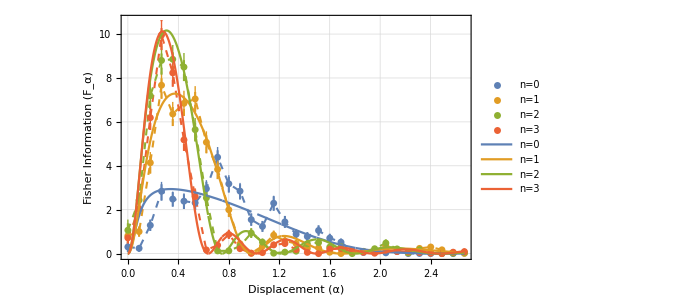

```mathematica
(*create summary figure*)
fisherDataMaximaFormatted
fisherFitMaximaFormatted
fisherInfoSummaryFigure=Show[
{
fisherDataPlot,
fisherFitPlot
},

PlotRange->{
{0.,1.},
{0.,Full}
}
]
```

# Sensitivity vs Interrogation Time - Batch

```mathematica
(*todo: add plotting return*)
```

```mathematica
(*specify directory*)
(*directoryString="/Users/claytonho/Documents/Research/Projects/Correlation Sampling/Data/2025_10_20_sensitivity_scaling";*)
directoryString="C:\\Users\\EGGS2\\Documents\\Correlation Sampling\\2025_10_21_sensitivity_scaling";
```

```mathematica
(*specify dataset RIDs*)
ridList=Join[
Range[135319,135354],
Range[135379,135418],
Range[135438,135477]
];
Length[ridList]
```

116

```mathematica
(*select valid time ranges*)
{minTimeValidus,maxTimeValidus}={1,2300};
```

## Configuration

Dataset Configuration:

```mathematica
countCol=2;(*raw count column*)
```

```mathematica
sweepCol=4;(*sweep column*)
```

Convert Units:

```mathematica
sweepUnits=1.*^-3;(*convert from sweep column to target units*)
```

Plotting Configuration:

```mathematica
xAxisLabel="Frequency (kHz)";(*x-axis label for sweep*)
```

```mathematica
figureTitle="Fock Linescan";(*plot title to set*)
```

## Process

## Process Function Special

```mathematica
(*process linescan datasets for sensitivity scaling figure*)
Clear[BatchProcessFitSensitivityScaling];
BatchProcessFitSensitivityScaling[rid_]:=Module[
{
datafileList=ImportDatasetARTIQ[directoryString,ToString[rid]],
dataset,parameters,ADJFix,CDJFix,
datasetProcessed,dsN,fitfunc,
fitRes,
dsPlotTMP,summaryFigure,fitParams
},

(*merge datasets and get parameter list*)
{dataset,parameters}=datafileList;

{ADJFix,CDJFix}=Switch[parameters["fock_num_prep"],
0,{0.926687,0.0059494},
1,{0.79492,0.077884},
2,{0.72353,0.117476},
3,{0.619214,0.18123}
];


datasetProcessed=ThresholdCounts[dataset[[;;,{sweepCol,countCol}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{sweepUnits,1}];
dsN=CollateDataSimple[
datasetProcessed[[;;,{1,2}]],
{1}
];
(*replace 0 uncertainty with 0.01*)
dsN[[;;,3]]=dsN[[;;,3]]/.{(0|0.)->0.01};

(*fit function and fix extra params*)
fitfunc=ADJFix*(1.-Exp[-#^2.]*LaguerreL[parameters["fock_num_prep"],#^2]^2.)+CDJFix&[
α0*Sinc[((δ-δ0)*tDJ)/2.*(wkhz*μs)+1.*^-8]
];

(*fit! and get results*)
fitRes=NonlinearModelFit[
dsN[[;;,{1,2}]],
fitfunc,

(*fit guesses*)
{
{α0,-Log[1.-Abs[Subtract@@MinMax[dsN[[;;,2]]]]]},
{δ0,First@dsN[[Ordering[dsN[[;;,2]],-1],1]]},(*linecenter*)
{tDJ,parameters["time_heating_us"]+0.5*parameters["time_pulse_shape_rolloff_us"]*parameters["enable_pulse_shaping"]}(*pulse time*)
},

(*fit parameter*)
δ,

(*fit weights*)
Weights->dsN[[;;,3]]^-2.
];


(*plot summary figure*)
dsPlotTMP=dsN[[;;,{1,2}]];
dsPlotTMP[[;;,2]]=Around@@@dsN[[;;,{2,3}]];
summaryFigure=Show[
{
ListPlot[
{
dsPlotTMP,dsPlotTMP
},
PlotRange->{
{Full,Full},
{0.,1.}
},

FrameLabel->{ 
{Style["D-5/2 Probability",{Black,Directive[15]}],None},
{
Style[xAxisLabel,{Black,Directive[15]}],
Style[StringForm[
"`` - RID: ``, n=``\nPulse Time: ``μs, Linecenter Precision: `` Hz",
"Fock Linescan",rid,parameters["fock_num_prep"],parameters["time_heating_us"],NumberForm[Abs[1000.*Subtract@@fitRes["ParameterConfidenceIntervals"][[2]]],5]
],
{Black,Directive[15]}]
}
},

PlotStyle->{Black},
ImageSize->{700,450},
AspectRatio->Full
],
Plot[
fitRes[δ],
{δ,dsN[[1,1]],dsN[[-1,1]]},
PlotRange->Full
]
}
];
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];

(*clear before returning*)
ClearInOut[];Clear[datafileList,dataset,datasetProcessed,dsN,dsPlotTMP];

(*return list of {fock_num, pulse_time, frequency_precision}*)
Return[{
parameters["fock_num_prep"],
parameters["time_heating_us"],
Abs[1000.*Subtract@@fitRes["ParameterConfidenceIntervals"][[2]]],

fitParams,
summaryFigure
}];
];
```

## Process Data

```mathematica
(*batch process*)
AbsoluteTiming[
dsRes=ParallelMap[
BatchProcessFitSensitivityScaling[#]&,
ridList
];
]
```

{2.11917,Null}

```mathematica
(*separate and sort datasets*)
dsSensitivityFock0=Sort[
Select[
dsRes,
((First[#]==0)&&(minTimeValidus<=#[[2]]<=maxTimeValidus))&
],
#1[[2]]<#2[[2]]&
][[;;,{2,3}]];
dsSensitivityFock1=Sort[
Select[
dsRes,
((First[#]==1)&&(minTimeValidus<=#[[2]]<=maxTimeValidus))&
],
#1[[2]]<#2[[2]]&
][[;;,{2,3}]];
dsSensitivityFock2=Sort[
Select[
dsRes,
((First[#]==2)&&(minTimeValidus<=#[[2]]<=maxTimeValidus))&
],
#1[[2]]<#2[[2]]&
][[;;,{2,3}]];
dsSensitivityFock3=Sort[
Select[
dsRes,
((First[#]==3)&&(minTimeValidus<=#[[2]]<=maxTimeValidus))&
],
#1[[2]]<#2[[2]]&
][[;;,{2,3}]];
```

```mathematica
(*group data into an association*)
dsSensitivityAll=<|
"n=0"->dsSensitivityFock0,
"n=1"->dsSensitivityFock1,
"n=2"->dsSensitivityFock2,
"n=3"->dsSensitivityFock3
|>;
```

## Plot

### Prepare Plotting

```mathematica
(*get number of datasets*)
numDatasets=Length[dsSensitivityAll];
(*format data for plotting*)
sensitivityScalePlotData=Riffle[#,#]&[Values[dsSensitivityAll]];
```

```mathematica
(*prepare plot styles*)
sensitivityScalingPlotStyles=Riffle@@Transpose[
{
{#,PointSize[0.010]},
{#,Dashed,Thickness[0.003]}
}&/@DefaultPlotColors[[;;numDatasets]]
];
sensitivityScalingPlotJoin=Riffle[
ConstantArray[False,numDatasets],
ConstantArray[True,numDatasets]
];
sensitivityScalePlotLegends=Riffle[
Keys[dsSensitivityAll],
ConstantArray[None,numDatasets]
];
```

### Plot Data!

```mathematica
(*plot processed data*)
sensitivityScalingPlot=ListLogLogPlot[
sensitivityScalePlotData,

(*PlotRange->{
{0.,Full},
{0.,Full}
},*)
PlotRange->Full,
FrameLabel->{ 
{Style[StringForm["``","Frequency Precision (95% CI, Hz)"],{Black,Directive[15]}],None},
{
Style[StringForm["``","Interrogation Time (μs)"],{Black,Directive[15]}],
Style[StringForm["``","Frequency Precision vs Interrogation Time"],{Black,Directive[15]}]
}
},

PlotStyle->sensitivityScalingPlotStyles,
Joined->sensitivityScalingPlotJoin,
PlotLegends->sensitivityScalePlotLegends,

ImageSize->Scaled[0.45]
];
```

## Show

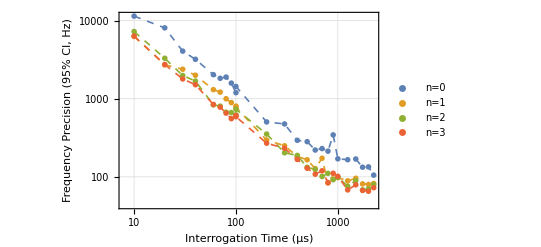

```mathematica
sensitivityScalingPlot
```

## Inspect

```mathematica
(*MatrixForm/@dsRes[[;;,{4,5}]]*)
```